```mathematica
SetDirectory[NotebookDirectory[]];
```

## Question 1 - handel again

### d)

```mathematica
handel=Transpose[Import["Files/handel.csv","Data"]][[1]]
```

{0,-0.0061568,-0.075036,-0.031169,0.0061568,0.038095,0.018855,-0.025012,-0.031169,-0.075036,-0.12583,-0.1443,-0.18124,-0.19048,-0.075036,-0.012698,-0.038095,-0.075036,0,0.075036,0.12583,0.18124,0.15046,0.12583,73065,-0.23973,-0.095046,-0.081193,-0.018855,0.081193,0.11967,0.12583,0.15661,0.095046,0.012698,0.13199,0.018855,-0.081193,-0.1443,-0.19048,-0.1443,-0.062722,0.018855,0.15046,0.16277,0.12583,0.22742,0.15046,0}
 |  |  |  |

```mathematica
handel3Avg=ListConvolve[Table[1/3,{3}],handel]
```

{-0.0270643,-0.0374539,-0.0333494,0.00436093,0.0210356,0.010646,-0.012442,-0.043739,-0.077345,-0.115055,-0.150457,-0.172007,73087,0.0232173,-0.0688793,-0.138658,-0.159693,-0.132501,-0.0627223,0.035531,0.110695,0.146353,0.172007,0.167903,0.12596}
 |  |  |  |

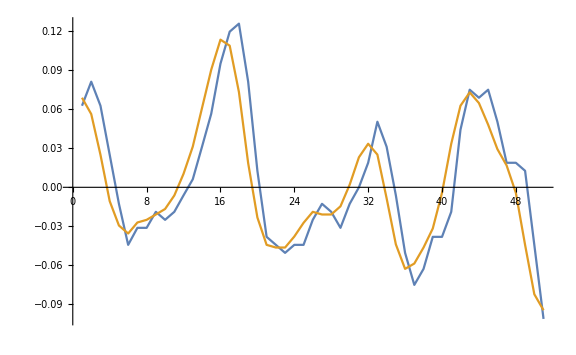

```mathematica
ListLinePlot[{handel[[1000;;1050]],handel3Avg[[1000;;1050]]},ImageSize->Large]
```

```mathematica
ListPlay[handel,SampleRate->8192]
ListPlay[handel3Avg,SampleRate->8192]
```

-Graphics-

-Graphics-

#### The avg sound sounds much more muffled and smoothed out than the original

### e)

```mathematica
Rasterize@ListLinePlot[Table[RotateRight[Abs[Fourier[data]],Floor@(Length[data]/2)],{data,{handel,handel3Avg}}],PlotRange->Full,ImageSize->Large]
```

-Graphics-

#### We can see in the above plot

## Question 2 - disturbance in the force

```mathematica
indexLargest[soundData_]:=(Position[Re[soundData],Max[Re[soundData]]][[1]])
NotchFilter[Ω0_,q_,Ω_]:=(((1−E^(−I(Ω0+Ω)))(1−E^(−I(Ω−Ω0))))/((1-q*E^(−I(Ω0+Ω)))(1−q*E^(−I(Ω−Ω0)))))
```

```mathematica
x275=Import["Files/Disturbance275.wav","Data"];
x261=Import["Files/Disturbance261.wav","Data"];
xOrig=Import["Files/DisturbanceOrig.wav","Data"];
Fs2=22050;
```

```mathematica
disturbances={x275,x261,xOrig};
names={"x275","x261","xOrig"};
```

```mathematica
Grid[{names,Table[ListPlay[soundData,SampleRate->Fs2],{soundData,disturbances}]}]
```

x275 | x261 | xOrig
-Graphics- | -Graphics- | -Graphics-

```mathematica
Rasterize@ListLinePlot[Table[RotateRight[Abs[Fourier[soundData]],Floor@(Length[soundData]/2)],{soundData,disturbances}],PlotRange->Full,ImageSize->Large]
```

-Graphics-

#### Two extreme values show in plot below. Set these to zero and get back sound data

{0.00409717-0.0021909 ⅈ,-0.00112833-0.001021 ⅈ,0.00182203-0.000320854 ⅈ,0.0000502204-0.000396673 ⅈ,-0.000673694+0.0024469 ⅈ,39992,0.0000502204+0.000396673 ⅈ,0.00182203+0.000320854 ⅈ,-0.00112833+0.001021 ⅈ,0.00409717+0.0021909 ⅈ}
 |  |  |  |

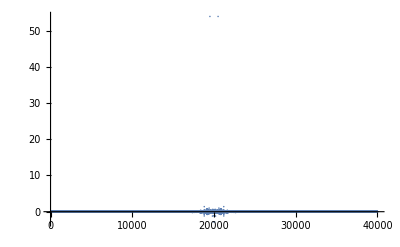

```mathematica
x275IDFT=RotateRight[Fourier[x275],Floor@(Length[x275]/2)]
ListPlot[Re[x275IDFT],PlotRange->All]
```

{0,0}

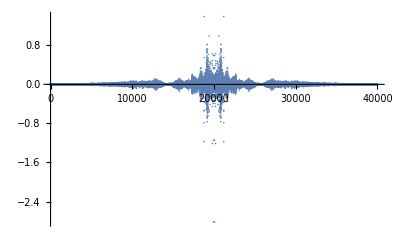

```mathematica
Table[x275IDFT[[indexLargest[x275IDFT]]]=0,{i,2}]
ListPlot[Re[x275IDFT],PlotRange->All]
```

```mathematica
ListPlay[Re[InverseFourier[RotateLeft[x275IDFT,Floor@(Length[x275IDFT]/2)]]],SampleRate->Fs2]
```

-Graphics-

### a) ii - Use notch filter to filter our noise

```mathematica
NotchFilter275=NotchFilter[(2*275.6181)/Fs2,.9,Ω]
```

((1-ⅇ^(-ⅈ (-0.0249994+Ω))) (1-ⅇ^(-ⅈ (0.0249994+Ω))))/((1-0.9 ⅇ^(-ⅈ (-0.0249994+Ω))) (1-0.9 ⅇ^(-ⅈ (0.0249994+Ω))))

```mathematica
x275Notch=InverseFourier@MapThread[Times,{Fourier[x275],MapThread[Times,{Range[-Pi,Pi,2Pi/Length[x275]][[2;;]],Table[NotchFilter275,{Ω,x275}]}]}]
```

{-0.0568023+0.678366 ⅈ,0.00505128+0.51225 ⅈ,39997,-0.151374+0.699253 ⅈ,-0.110653+0.749577 ⅈ}
 |  |  |  |

```mathematica
ListPlay[Re[x275Notch],SampleRate->Fs2]
```

-Graphics-

```mathematica
y[n]=Ay[n−1]+By[n−2]+Px[n]+Qx[n−1]+Rx[n−2]
```

Ay[-1+n]+By[-2+n]+Px[n]+Qx[-1+n]+Rx[-2+n]

```mathematica
A=2q cos(Ω0)
B=−q^2
P=1
Q=-2Cos[
```